```mathematica
(*Open file selector dialog*)fileDialogResult=SystemDialogInput["FileOpen","*.csv"];
data=Import[fileDialogResult,"CSV","SkipLines"->1];
```

```mathematica
fs=250;
```

```mathematica
(*Get timestamps in seconds*)timestepDiv=1000000000;
tims=(data[[All,1]]-data[[1,1]])/timestepDiv;

(*Extract x,y,z data*)
{x,y,z}=Transpose[data[[All,2;;4]]];
```

```mathematica
(*ListLinePlot[Transpose[{tims,z}]]*)
```

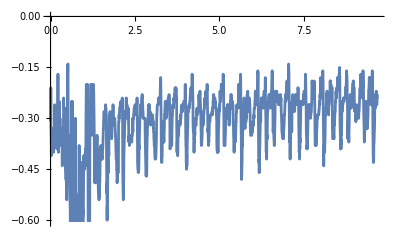

-Graphics-

-Graphics-

```mathematica
(*Resample data*)
Xdata=TimeSeriesResample[Transpose[{tims,x}],1/fs];
ListLinePlot[Xdata]
Ydata=TimeSeriesResample[Transpose[{tims,y}],1/fs];
ListLinePlot[Xdata]
Zdata=TimeSeriesResample[Transpose[{tims,z}],1/fs];
ListLinePlot[Xdata]
```

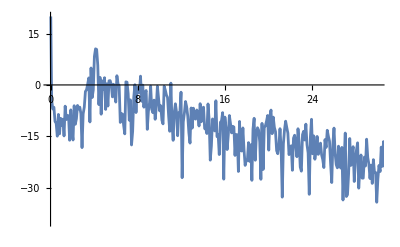

```mathematica
fftX=Abs[Fourier[Xdata[[All,2]]]];
Periodogram[Zdata[[All,2]],SampleRate->fs,PlotRange->{{0,30},{-40,20}}]
```

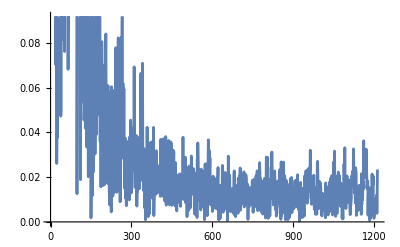

2423

2423

```mathematica
ListLinePlot[fftX[[1;;Floor[Length[fftX]/2]+1]]]
plotdata=fftX[[1;;Floor[Length[fftX]/2]+1]];
Length[Xdata]
Length[fftX]
```

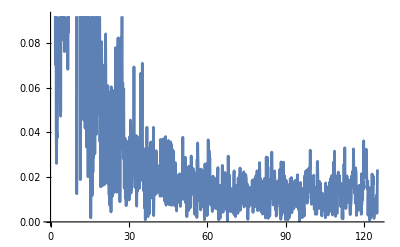

```mathematica
(*x=Range[1/fs,fs/2,fs/Floor[Length[fftX]/2]];*)
x=N@Subdivide[1/fs,fs/2,Floor[Length[fftX]/2]];
ListLinePlot[Transpose[{x,plotdata}]]
```

```mathematica
Length[x]
Length[plotdata]
```

1212

1212

```mathematica
(*FFT function*)
fftMaker[data_,Fs_]:=Module[{L,NFFT,fftdata,freq,pwr},L=Length[data];
NFFT=2^Ceiling[Log2[L]];(*Next power of 2 from length of the data*)fftdata=Fourier[data,FourierParameters->{-1,1}]/L;
pwr=2*Abs[fftdata[[1;;Ceiling[NFFT/2]+1]]];
freq=Fs/2*Range[0,1,1/NFFT][[;;Ceiling[NFFT/2]+1]];
{freq,pwr}]

(*Compute FFT and plot*)
{fXfreq,fXpwr}=fftMaker[Xdata-Mean[Xdata],Fs];
{fYfreq,fYpwr}=fftMaker[Ydata-Mean[Ydata],250];
{fZfreq,fZpwr}=fftMaker[Zdata-Mean[Zdata],250];

ListLinePlot[{fXfreq,#}ᵀ&/@{fXpwr,fYpwr,fZpwr},PlotRange->{{0,25},Automatic},Frame->True,FrameLabel->{"Frequency (Hz)","Power Spectrum"},PlotLegends->{"X","Y","Z"}]
```

```mathematica
ListLinePlot[Series[x,{x,0,10}]]
```